```mathematica
ClearAll["Global`*"]

wd=SetDirectory@NotebookDirectory[]

styles={Directive[RGBColor[0,0,0],AbsoluteThickness[4]],Directive[RGBColor[0.9,0,0],AbsoluteThickness[3],AbsoluteDashing[Medium]],Directive[RGBColor[0,0,0.5],AbsoluteThickness[2],AbsoluteDashing[{10,5}]],Directive[RGBColor[0,0.5,0],AbsoluteThickness[2],AbsoluteDashing[{10,5,2,5}]],Directive[RGBColor[1,0.5,0.0],AbsoluteThickness[2],AbsoluteDashing[{1,4}]],Directive[RGBColor[0.5,0.5,0.5],AbsoluteThickness[2],AbsoluteDashing[{1,4}]]};

FrameTicksFontSize=20;
FrameFontSize=20;PlotOptions={Axes->False,Frame->True,FrameTicksStyle->{Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Times"],Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Times"]},FrameStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]]},AspectRatio->0.75,ImageSize->Medium,PlotStyle->styles,PlotRange->All};
SetOptions[Plot,PlotOptions];
SetOptions[LogPlot,PlotOptions];
SetOptions[LogLogPlot,PlotOptions];
SetOptions[LogLinearPlot,PlotOptions];
SetOptions[ListPlot,PlotOptions];
SetOptions[PolarPlot,PlotOptions];

Nf=3;
eg=16Pi^2/30;
eq=6*3*7Pi^2/120;  (*check these later*)
sFac = eg+eq 

%*1.0

rationalPolyFit[data_,NN_,MM_]:=Module[{a,b,varsa,varsb,vars,sol,varsc,varsd,Q},
varsa=Table[a[n],{n,0,NN}];
varsb=Table[b[m],{m,0,MM}];
vars=Join[varsa,varsb];
sol=FindFit[data,Sum[a[n]x^n,{n,0,NN}]/Sum[b[m]x^m,{m,0,MM}],vars,x,MaxIterations->10000];
varsc=varsa/.sol;
varsd=varsb/.sol;
Return[Sum[varsc[[n+1]]x^n,{n,0,NN}]/Sum[varsd[[m+1]]x^m,{m,0,MM}]];
];
```

/Users/Michael/Desktop/bjorken_vahydro/mathematica

(19 π^2)/12

15.6269

```mathematica
eosDataRaw=Import[wd<>"/eos.dat"];
eosData= Take[eosDataRaw,{3,Length[eosDataRaw]}];

(* Subscript[ϵ, eq](T) *)
LogEDLogTInt = Interpolation[eosData[[All,{1,2}]]];
edInt[T_] = 10^LogEDLogTInt[Log[10,T]];

(* Subscript[P, eq](T) *)
LogPLogTInt = Interpolation[eosData[[All,{1,4}]]];
PInt[T_] = 10^LogPLogTInt[Log[10,T]];


LogdPLogEdInt = Interpolation[eosData[[All,{2,5}]]];
dPIntE[e_]=10^LogdPLogEdInt[Log[10,e]];
LogdELogEdInt = Interpolation[eosData[[All,{2,3}]]];
dEIntE[e_]=10^LogdELogEdInt[Log[10,e]];

cs2Int[T_] = dPIntE[edInt[T]]/dEIntE[edInt[T]];


(* z = m/T *)

(*zInt[T_]=√((1+edInt[T]/PInt[T])/cs2Int[T]*(1.0-3.0*cs2Int[T]));*)
(*zInt[T_]=√(12.0*(1.0-3.0*cs2Int[T]));

zdata=Table[{T,zInt[T]},{T,0.001,5,0.0005}];

n = 23;

z[T_]=rationalPolyFit[zdata,n,n]/.{x->T};
Grid[{{Plot[{zInt[T],z[T]},{T,0.001,5},PlotStyle->styles,ImageSize->550,Frame->True,Axes->False,PlotLabel->Style["z(T)",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[z[T]/zInt[T]-1.0]},{T,0.001,5},PlotStyle->styles,ImageSize->550,Frame->True,Axes->False,PlotLabel->Style["|z_fit/z - 1|",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
z[T]//CForm*)
```

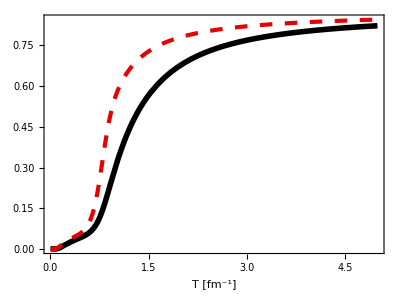

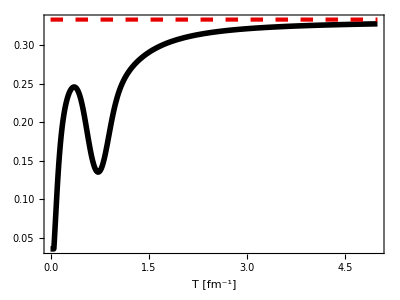

```mathematica
Plot[{PInt[T]/(sFac T^4/3),edInt[T]/(sFac T^4)},{T,.001,5},PlotStyle->styles,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]

Plot[{cs2Int[T],1/3},{T,0,5},PlotStyle->styles,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]
```

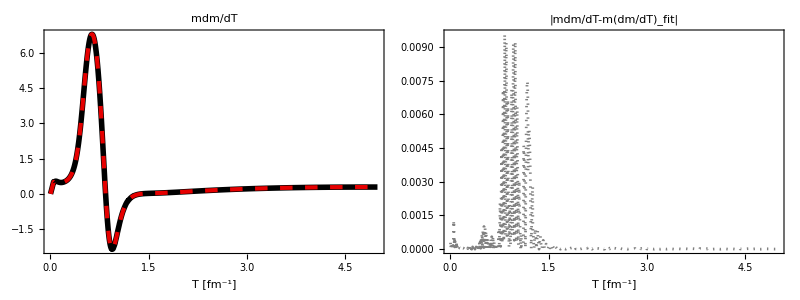

```mathematica
(* m * dm/dT *)

massInt[T_]=T*zInt[T];

mdmdTInt[T_]=massInt[T]*massInt'[T];

mdmdTdata=Table[{T,mdmdTInt[T]},{T,0.001,5,0.0008}];

n = 17;

mdmdT[T_]=rationalPolyFit[mdmdTdata,n,n]/.{x->T};
Grid[{{Plot[{mdmdTInt[T],mdmdT[T]},{T,0.001,5},PlotStyle->styles,ImageSize->550,Frame->True,PlotLabel->Style["mdm/dT",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[mdmdTInt[T]-mdmdT[T]]},{T,0.001,5},PlotStyle->styles,ImageSize->550,Frame->True,PlotLabel->Style["|mdm/dT-m(dm/dT)_fit|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
```

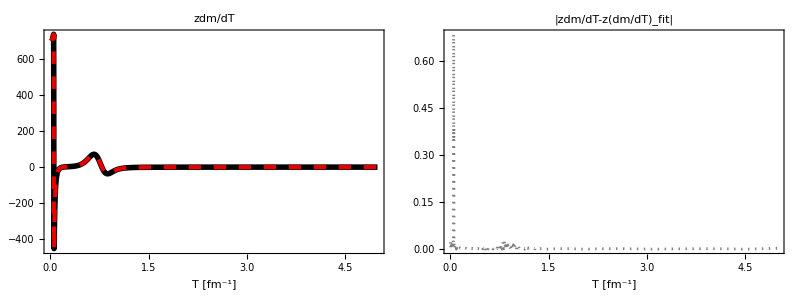

(0.0037551339654934377 - 0.5862233593513403*T + 41.071727723978235*Power(T,2) - 1714.7875560435307*Power(T,3) + 47925.52105150097*Power(T,4) - 
     957671.7219220655*Power(T,5) + 1.4269172655442191e7*Power(T,6) - 1.619137625369596e8*Power(T,7) + 1.3926398828988779e9*Power(T,8) - 
     8.807434673634623e9*Power(T,9) + 3.919620189191995e10*Power(T,10) - 1.1820787252125908e11*Power(T,11) + 2.3472463909721664e11*Power(T,12) - 
     2.9600958390373376e11*Power(T,13) + 2.2735208795984885e11*Power(T,14) - 9.962063384597006e10*Power(T,15) + 2.1690252973196064e10*Power(T,16) - 
     1.6778600723692982e9*Power(T,17))/
   (5.227963284926312e-6 - 0.0008082562200005168*T + 0.05486294539506078*Power(T,2) - 2.0813434359988303*Power(T,3) + 42.90969618142504*Power(T,4) - 
     122.7078799005385*Power(T,5) - 22351.240804622455*Power(T,6) + 807055.6606803666*Power(T,7) - 1.5844421352370625e7*Power(T,8) + 
     2.0113439948641732e8*Power(T,9) - 1.6843333030055444e9*Power(T,10) + 9.089715271877333e9*Power(T,11) - 3.0623785070687508e10*Power(T,12) + 
     6.5054732233006905e10*Power(T,13) - 8.761865869627203e10*Power(T,14) + 7.29636208812097e10*Power(T,15) - 3.444798172523424e10*Power(T,16) + 
     7.087681095910018e9*Power(T,17))

```mathematica
(* z × dm/dT *)


zdmdTInt[T_] = zInt[T] * dmdTInt[T];


zdmdTdata=Table[{T,zdmdTInt[T]},{T,0.001,5,0.0008}];

n = 17;

zdmdT[T_]=rationalPolyFit[zdmdTdata,n,n]/.{x->T};
Grid[{{Plot[{zdmdTInt[T],zdmdT[T]},{T,0.001,5},PlotStyle->styles,ImageSize->550,Frame->True,PlotLabel->Style["zdm/dT",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[dmdTInt[T]-dmdT[T]]},{T,0.001,5},PlotStyle->styles,ImageSize->550,Frame->True,PlotLabel->Style["|zdm/dT-z(dm/dT)_fit|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

zdmdT[T]//CForm
```

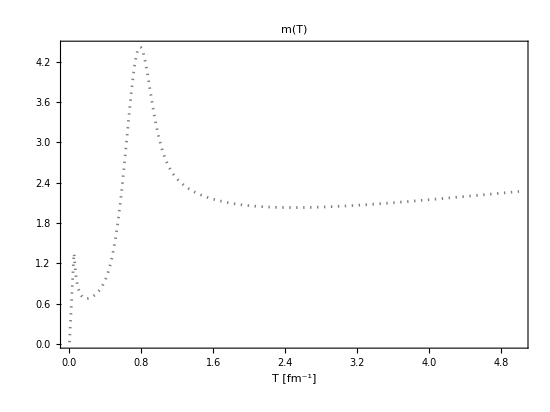

```mathematica
Plot[{massInt[T]},{T,0.001,5},PlotStyle->styles,ImageSize->550,Frame->True,PlotLabel->Style["m(T)",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]
```

(19 π^4)/36

15.6269

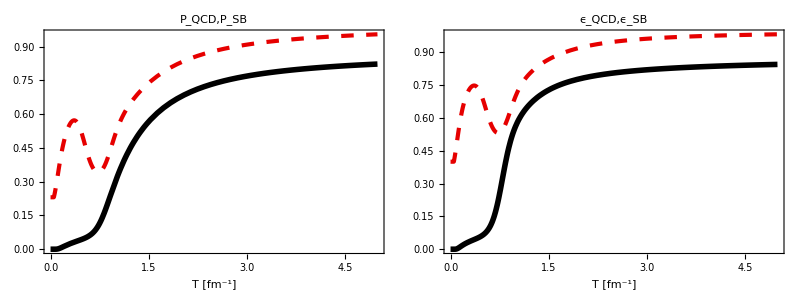

```mathematica
nc = 3;
nf = 3;
g =Pi^4/180*(4*(nc^2-1)+7*nc*nf)



3.*g/Pi^2
Peq[T_]=(g*T^4)/(2.0*Pi^2)*zInt[T]^2*BesselK[2,zInt[T]];
Eeq[T_]=(g*T^4)/(2.0*Pi^2)*zInt[T]^2*(3.0*BesselK[2,zInt[T]]+zInt[T]*BesselK[1,zInt[T]]);

(*Peq[T_] =(g*T^4)/Pi^2;

Eeq[T_]=(3.0*g*T^4)/Pi^2;*)

Grid[{{Plot[{PInt[T]/(sFac T^4/3),Peq[T]/(sFac T^4/3)},{T,.00,5},PlotStyle->styles,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"P_QCD,P_SB",BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{edInt[T]/(sFac T^4),Eeq[T]/(sFac T^4)},{T,.00,5},PlotStyle->styles,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"ϵ_QCD,ϵ_SB",BaseStyle->{FontSize->16},AspectRatio->0.75]
}}]

Plot[{Peq[T]/PInt[T],1},{T,01,5},PlotStyle->styles,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"P_eq/P_QCD",BaseStyle->{FontSize->16},AspectRatio->0.75];
```

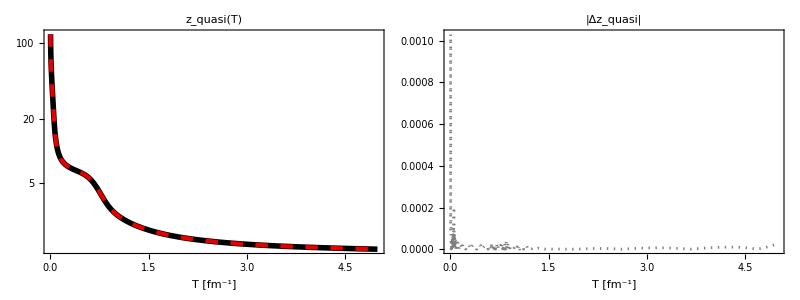

(2.195527549421445e-14 + 5.014273212142939e-11*T + 6.8769768080936324e-9*Power(T,2) - 1.3090323372462384e-6*Power(T,3) + 
     0.00007503723419734601*Power(T,4) - 0.0019335423100477788*Power(T,5) + 0.0077581370622797526*Power(T,6) + 1.0840238709953247*Power(T,7) - 
     40.41237726417249*Power(T,8) + 815.5709414412947*Power(T,9) - 11117.3113417968*Power(T,10) + 107720.35990943392*Power(T,11) - 
     727161.0603316505*Power(T,12) + 3.12288627176472e6*Power(T,13) - 7.240727201149486e6*Power(T,14) + 8.813651470346985e6*Power(T,15) - 
     3.535759885234317e6*Power(T,16) - 5.454281769326236e6*Power(T,17) + 1.0415987187648855e7*Power(T,18) - 8.0189396235499745e6*Power(T,19) + 
     2.6430627991581215e6*Power(T,20))/
   (1.1541703277540495e-16 + 4.122377967105372e-13*T + 1.2528690762234088e-10*Power(T,2) - 1.1203883703791743e-8*Power(T,3) - 
     3.65428489042621e-8*Power(T,4) + 0.00004068369176438496*Power(T,5) - 0.0024580222716044254*Power(T,6) + 0.08433957015198745*Power(T,7) - 
     2.0279246693088906*Power(T,8) + 36.56366190486074*Power(T,9) - 490.05025567116945*Power(T,10) + 4477.3308927313055*Power(T,11) - 
     21467.525530376926*Power(T,12) - 23929.310531648207*Power(T,13) + 889228.088912891*Power(T,14) - 4.262596231414713e6*Power(T,15) + 
     1.0642287968093066e7*Power(T,16) - 1.643826578603126e7*Power(T,17) + 1.6160269998993594e7*Power(T,18) - 9.40765741315934e6*Power(T,19) + 
     2.502796051035953e6*Power(T,20))

```mathematica
SInt[T_] = (edInt[T]+PInt[T])/T;
nc = 3.0;
nf = 3.0;
g =Pi^4/180.0*(4.0*(nc^2-1.0)+7.0*nc*nf);
F[T_]=(2.0*Pi^2)/g*SInt[T]/T^3;

zQuasi=Table[{T,""},{T,0.001,5.0,0.0005}];

zQuasi[[1,2]]=121.13801765177428;

For[i = 2, i ≤Length[zQuasi],i++,
zQuasi[[i,2]]=x/.FindRoot[x^3*BesselK[3,x]==F[zQuasi[[i,1]]],{x,zQuasi[[i-1,2]]},MaxIterations->2000];
]

zQuasifunc=Interpolation[zQuasi];


zQuasidata=Table[{T,zQuasifunc[T]},{T,0.001,5.0,0.0005}];

n = 20;

zQuasifit[T_]=rationalPolyFit[zQuasidata,n,n]/.{x->T};




Grid[{{
LogPlot[{zQuasifunc[T],zQuasifit[T]},{T,0.001,5},PlotStyle->styles,ImageSize->400,Frame->True,PlotLabel->Style["z_quasi(T)",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],

Plot[{Abs[zQuasifunc[T]-zQuasifit[T]]},{T,0.001,5},PlotStyle->styles,ImageSize->400,Frame->True,PlotLabel->Style["|Δz_quasi|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

zQuasifit[T]//CForm
```

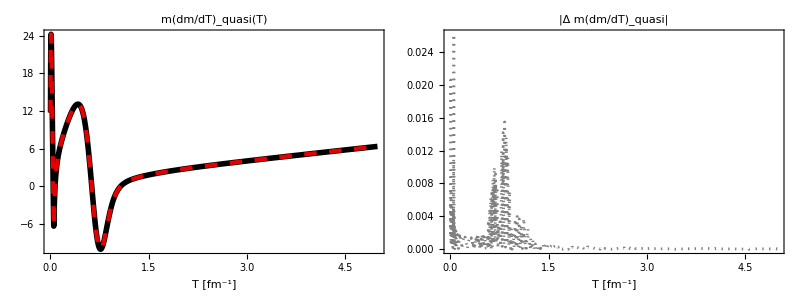

(6.816033132910849e-10 + 1.7790915724868891e-6*T - 0.00030685573686689566*Power(T,2) + 0.023473842070213607*Power(T,3) - 
     1.0732881083537456*Power(T,4) + 32.832198021861664*Power(T,5) - 709.7072077947313*Power(T,6) + 11127.167196570503*Power(T,7) - 
     127334.34497884315*Power(T,8) + 1.0505151080327253e6*Power(T,9) - 6.040988782373799e6*Power(T,10) + 2.2838438268810038e7*Power(T,11) - 
     5.285418442808765e7*Power(T,12) + 7.498857047120465e7*Power(T,13) - 6.56141265603832e7*Power(T,14) + 3.244851452301533e7*Power(T,15) - 
     4.306248519325042e6*Power(T,16) - 4.246216963572507e6*Power(T,17) + 1.8321297087034914e6*Power(T,18))/
   (1.6642262354933514e-10 + 2.392737679464936e-8*T - 5.770833446723635e-6*Power(T,2) + 0.00047650968449680815*Power(T,3) - 
     0.02381082180560632*Power(T,4) + 0.8393191062044852*Power(T,5) - 22.059270410143014*Power(T,6) + 436.7671455149582*Power(T,7) - 
     6431.104009203983*Power(T,8) + 68566.51769617059*Power(T,9) - 509112.8351052782*Power(T,10) + 2.5006513314870317e6*Power(T,11) - 
     7.741180724418022e6*Power(T,12) + 1.5432809530797705e7*Power(T,13) - 2.021565552418443e7*Power(T,14) + 
     1.7198582484739084e7*Power(T,15) - 8.803186353145795e6*Power(T,16) + 2.1173893883225573e6*Power(T,17) - 25629.370279979517*Power(T,18))

```mathematica
mQuasifunc[T_] =T*zQuasifunc[T]; 

mdmdTQuasi[T_] = mQuasifunc[T] * mQuasifunc'[T];


mdmdTQuasidata=Table[{T,mdmdTQuasi[T]},{T,0.001,5,0.0004}];

n = 18;

mdmdTQuasifit[T_]=rationalPolyFit[mdmdTQuasidata,n,n]/.{x->T};

Grid[{{
Plot[{mdmdTQuasi[T],mdmdTQuasifit[T]},{T,0.001,5},PlotStyle->styles,ImageSize->500,Frame->True,PlotLabel->Style["m(dm/dT)_quasi(T)",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],

Plot[{Abs[mdmdTQuasi[T]-mdmdTQuasifit[T]]},{T,0.001,5},PlotStyle->styles,ImageSize->500,Frame->True,PlotLabel->Style["|Δ m(dm/dT)_quasi|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

mdmdTQuasifit[T]//CForm
```

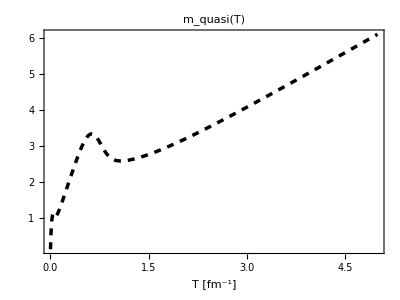

```mathematica
Plot[{mQuasifunc[T]},{T,0.001,5},PlotStyle->Directive[RGBColor[0,0,0],AbsoluteThickness[2.5],Dashed],ImageSize->400,Frame->True,PlotLabel->Style["m_quasi(T)",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]
```

```mathematica
dmdTQuasi[T_]=mQuasifunc'[T];


H[T_] := -(g*T^3*zQuasifunc[T]^2*BesselK[1,zQuasifunc[T]]*dmdTQuasi[T])/(2.0*Pi^2);

HQuasi=Table[{T,""},{T,0.001,5.0,0.0005}];
B0Quasi=Table[{T,""},{T,0.001,5.0,0.0005}];

For[i = 1, i ≤Length[HQuasi],i++,

Tprime = HQuasi[[i,1]];
HQuasi[[i,2]]= H[Tprime];
]

Hfunc=Interpolation[HQuasi]


B0Quasi[[1,2]] = 0.0;


For[i = 2, i ≤Length[B0Quasi],i++,
B0Quasi[[i,2]]= B0Quasi[[i-1,2]] + NIntegrate[Hfunc[Tprime],{Tprime,B0Quasi[[i-1,1]],B0Quasi[[i,1]]}];
]


B0Quasifunc=Interpolation[B0Quasi];
```

InterpolatingFunction[{{0.001,5.}},<>]

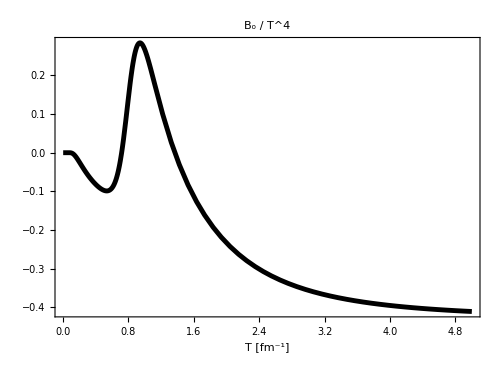

```mathematica
Plot[{B0Quasifunc[T]/T^4},{T,.001,5},PlotStyle->{Black,Thickness[0.007]},ImageSize->500,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"B_o / T^4",BaseStyle->{FontSize->16},AspectRatio->0.75]
```

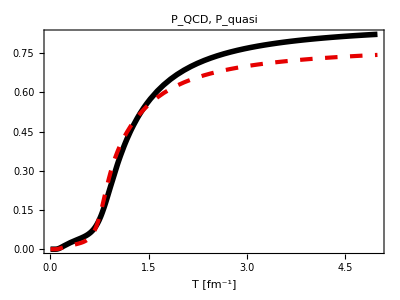
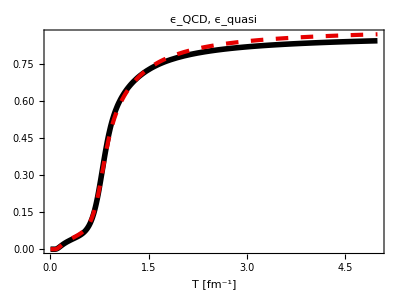
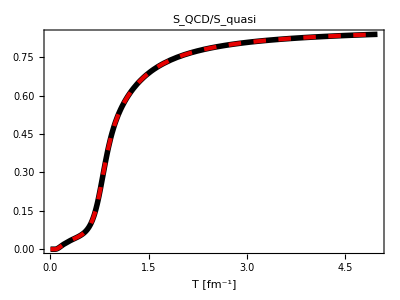
-Graphics- | -Graphics-
-Graphics- |

```mathematica
Pquasi[T_]=(g*T^4)/(2.0*Pi^2)*zQuasifunc[T]^2*BesselK[2,zQuasifunc[T]] (*-0*B0Quasifunc[T]*) ;
Equasi[T_]=(g*T^4)/(2.0*Pi^2)*zQuasifunc[T]^2*(3.0*BesselK[2,zQuasifunc[T]]+zQuasifunc[T]*BesselK[1,zQuasifunc[T]])(*+B0Quasifunc[T]*);

SQuasi[T_]=(Pquasi[T]+Equasi[T])/T;

Grid[{{Plot[{PInt[T]/(sFac T^4/3),Pquasi[T]/(sFac T^4/3)},{T,.001,5},PlotStyle->styles,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"P_QCD, P_quasi",BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{edInt[T]/(sFac T^4),Equasi[T]/(sFac T^4)},{T,.001,5},PlotStyle->styles,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"ϵ_QCD, ϵ_quasi",BaseStyle->{FontSize->16},AspectRatio->0.75]},
{Plot[{SInt[T]/(4*sFac*T^3/3),SQuasi[T]/(4*sFac*T^3/3)},{T,.001,5},PlotStyle->styles,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"S_QCD/S_quasi",BaseStyle->{FontSize->16},AspectRatio->0.75]
}}]
```

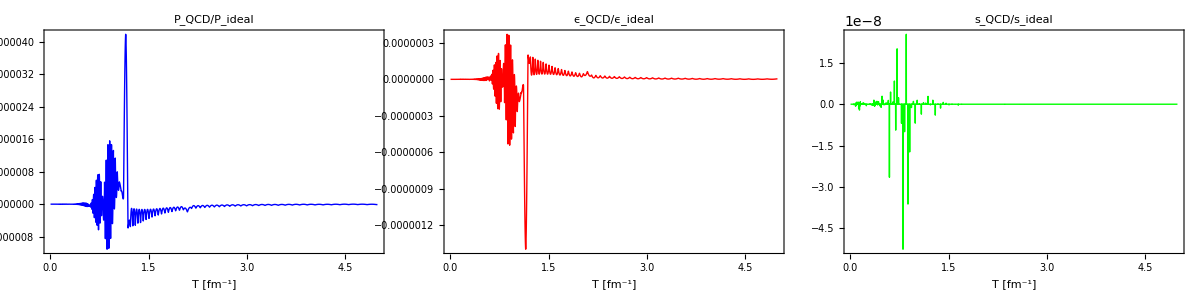

```mathematica
Grid[{{Plot[{(PInt[T]-Pquasi[T])/(sFac T^4/3)},{T,.001,5},PlotStyle->Blue,ImageSize->380,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"P_QCD/P_ideal",BaseStyle->{FontSize->18},AspectRatio->0.75],
Plot[{(edInt[T]-Equasi[T])/(sFac T^4)},{T,.001,5},PlotStyle->Red,ImageSize->380,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"ϵ_QCD/ϵ_ideal",BaseStyle->{FontSize->18},AspectRatio->0.75],Plot[{(SInt[T]-SQuasi[T])/(4*sFac T^4/3)},{T,.001,5},PlotStyle->Green,ImageSize->380,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"s_QCD/s_ideal",BaseStyle->{FontSize->18},AspectRatio->0.75]
}}]
```

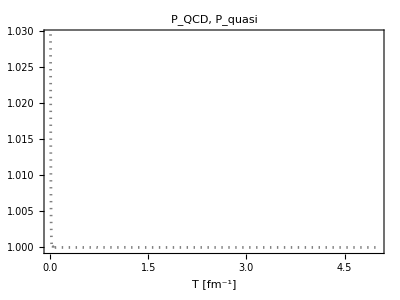

```mathematica
Plot[{PInt[T]/Pquasi[T]},{T,.01,5},PlotStyle->styles,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"P_QCD, P_quasi",BaseStyle->{FontSize->16},AspectRatio->0.75]
```

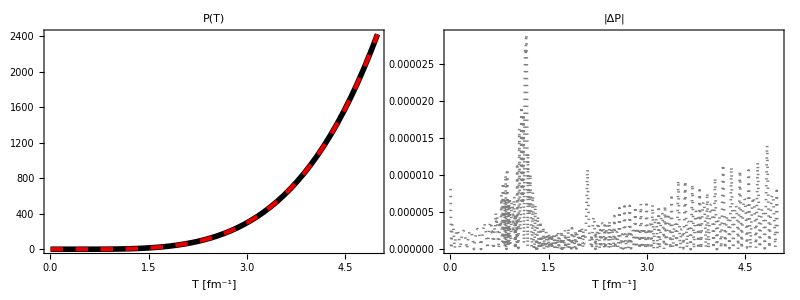

(-0.060736912198379976 + 6.988336708582318*T - 221.65119613024967*Power(T,2) + 3227.622321307183*Power(T,3) - 
     26102.004992202532*Power(T,4) + 128996.73427993082*Power(T,5) - 416886.1407762561*Power(T,6) + 905937.525583636*Power(T,7) - 
     1.31539760775123e6*Power(T,8) + 1.2230531361499897e6*Power(T,9) - 653662.4515639542*Power(T,10) + 144896.36540875357*Power(T,11) + 
     7602.524837867971*Power(T,12))/
   (-6683.304218484808 + 47495.99127908754*T - 153387.07374843178*Power(T,2) + 301121.43641707004*Power(T,3) - 
     393602.38201718463*Power(T,4) + 343366.99151144427*Power(T,5) - 183729.5358732759*Power(T,6) + 46302.41762071599*Power(T,7) - 
     397.28132020047036*Power(T,8) + 321.62173972893066*Power(T,9) - 31.399589208930866*Power(T,10) + 1.896580113127886*Power(T,11) - 
     0.052868593375905534*Power(T,12))

```mathematica
Pquasi[T_]=(g*T^4)/(2.0*Pi^2)*zQuasifunc[T]^2*BesselK[2,zQuasifunc[T]];  (*kinetic only; no bag term*)


Pquasidata=Table[{T,Pquasi[T]},{T,0.001,5,0.0005}];

n = 12;

Pquasifit[T_]=rationalPolyFit[Pquasidata,n,n]/.{x->T};

Grid[{{
Plot[{Pquasi[T],Pquasifit[T]},{T,0.001,5},PlotStyle->styles,ImageSize->500,Frame->True,PlotLabel->Style["P(T)",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],

Plot[{Abs[Pquasi[T]-Pquasifit[T]]},{T,0.001,5},PlotStyle->styles,ImageSize->500,Frame->True,PlotLabel->Style["|ΔP|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

Pquasifit[T]//CForm
```

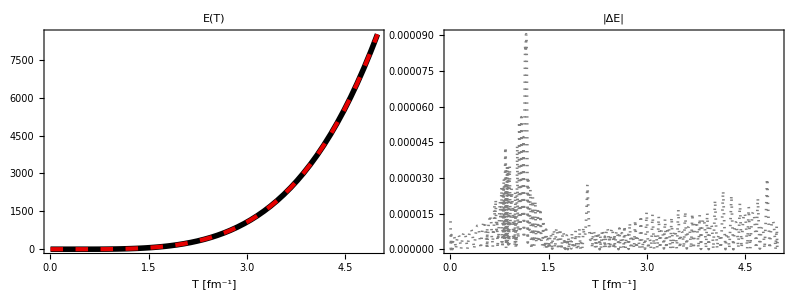

(0.00009491684322244673 - 0.02361379050334422*T + 1.3797449684199115*Power(T,2) - 33.82886830786682*Power(T,3) + 
     440.1303217026217*Power(T,4) - 3371.5358373636445*Power(T,5) + 16005.535555573097*Power(T,6) - 49862.71243687168*Power(T,7) + 
     104848.21092334883*Power(T,8) - 148253.7236840333*Power(T,9) + 135623.7414817843*Power(T,10) - 72796.06845179314*Power(T,11) + 
     17516.277968272858*Power(T,12))/
   (-6.0801761470907785 - 92.02868632549578*T + 900.1072873084156*Power(T,2) - 3406.550805299837*Power(T,3) + 7503.906637596268*Power(T,4) - 
     10625.464014402616*Power(T,5) + 9692.148179782494*Power(T,6) - 5257.106451479053*Power(T,7) + 1316.2231944400535*Power(T,8) - 
     12.72184898938659*Power(T,9) + 1.3330012931455673*Power(T,10) - 0.07856195382532238*Power(T,11) + 0.002090630483135667*Power(T,12))

```mathematica
Equasi[T_]=(g*T^4)/(2.0*Pi^2)*zQuasifunc[T]^2*(3.0*BesselK[2,zQuasifunc[T]]+zQuasifunc[T]*BesselK[1,zQuasifunc[T]]);  (*kinetic only; no bag term*)


Equasidata=Table[{T,Equasi[T]},{T,0.001,5,0.0008}];

n = 12;

Equasifit[T_]=rationalPolyFit[Equasidata,n,n]/.{x->T};


Grid[{{
Plot[{Equasi[T],Equasifit[T]},{T,0.001,5},PlotStyle->styles,ImageSize->500,Frame->True,PlotLabel->Style["E(T)",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],

Plot[{Abs[Equasi[T]-Equasifit[T]]},{T,0.001,5},PlotStyle->styles,ImageSize->500,Frame->True,PlotLabel->Style["|ΔE|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

Equasifit[T]//CForm
```

```mathematica
edInt[0.154*5.067731] /5.067731
```

0.343873